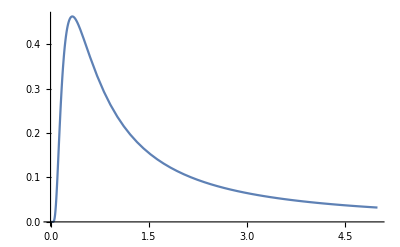

```mathematica
Plot[PDF[InverseGammaDistribution[0.5,0.5],x],{x,0,5}]
```

```mathematica
Expectation[z,z\[Distributed] TransformedDistribution[x*y,{x\[Distributed] InverseGammaDistribution[0.5,0.5],y\[Distributed] InverseGammaDistribution[10.0,10.0]}]]
```

-1.11111

```mathematica
Integrate[x*PDF[GammaDistribution[a,1/z],x],{x,lower,∞},Assumptions-> {lower>0,z>0,a>0}]
```

Gamma[1+a,lower z]/(z Gamma[a])

```mathematica
Integrate[x^2*PDF[GammaDistribution[a,1/z],x],{x,lower,∞},Assumptions-> {lower>0,z>0,a>0}]
```

Gamma[2+a,lower z]/(z^2 Gamma[a])

```mathematica
Solve[Gamma[1+a,lower z]/(z Gamma[a])==μ&&Gamma[2+a,lower z]/(z^2 Gamma[a])==v,{a,z},PositiveReals,Assumptions->{μ>0,lower>0,v>0}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Gamma[1+a,lower z]/(z Gamma[a])==μ&&Gamma[2+a,lower z]/(z^2 Gamma[a])==v,{a,z},,Assumptions→{μ>0,lower>0,v>0}]

check the mean

```mathematica
Gamma[1+a,lower z]/(z Gamma[a])/.{a->1.0,z->3.0,lower->0.0}
```

0.333333

check the variance

```mathematica
Gamma[2+a,lower z]/(z^2 Gamma[a])-(Gamma[1+a,lower z]/(z Gamma[a]))^2/.{a->1.0,z->3.0,lower->0.0}
```

0.111111

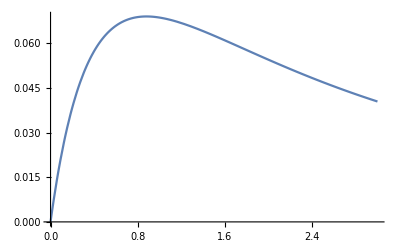

```mathematica
Plot[Variance[BetaDistribution[1.5,δ]],{δ,0,3}]
```